```mathematica
SetDirectory[NotebookDirectory[]];
```

## Uloha 2

{{u[t]→1+t+t^2+t^4}}

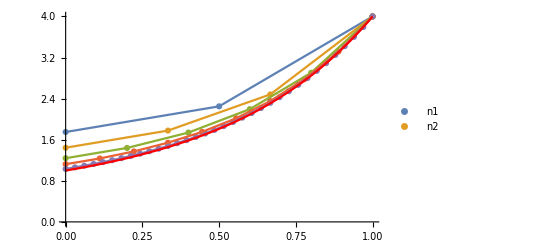

```mathematica
n1 = Import["./outputs/uloha2_finite_difference_neumman_simple_1n.csv","CSV"];
n2 = Import["./outputs/uloha2_finite_difference_neumman_simple_2n.csv","CSV"];
n4 = Import["./outputs/uloha2_finite_difference_neumman_simple_4n.csv","CSV"];
n8 = Import["./outputs/uloha2_finite_difference_neumman_simple_8n.csv","CSV"];
n16 = Import["./outputs/uloha2_finite_difference_neumman_simple_16n.csv","CSV"];
n32 = Import["./outputs/uloha2_finite_difference_neumman_simple_32n.csv","CSV"];
DSolve[{u''[t]==12 t^2+2, u'[0]==1, u[1]==4},u[t], t]
Show[
ListPlot[{n1, n2, n4, n8, n32}, PlotLegends->{"n1", "n2"}],
ListLinePlot[{n1, n2, n4, n8, n32}],
Plot[Evaluate[u[t]/.%],{t,0,1}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 3

{{u[t]→1+t+t^2+t^4}}

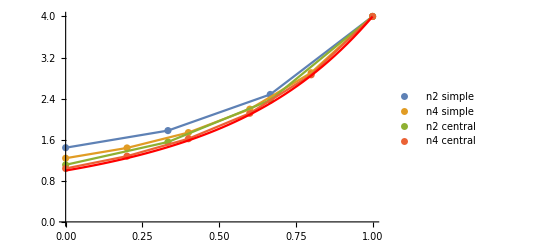

```mathematica
n2 = Import["./outputs/uloha2_finite_difference_neumman_simple_2n.csv","CSV"];
n4 = Import["./outputs/uloha2_finite_difference_neumman_simple_4n.csv","CSV"];
n22 = Import["./outputs/uloha2_finite_difference_neumman_central_2n.csv","CSV"];
n24 = Import["./outputs/uloha2_finite_difference_neumman_central_4n.csv","CSV"];
DSolve[{u''[t]==12 t^2+2, u'[0]==1, u[1]==4},u[t], t]
Show[
ListPlot[{n2, n4, n22, n24}, PlotLegends->{"n2 simple", "n4 simple", "n2 central" ,"n4 central"}],
(*ListLinePlot[{n2, n4, n22, n24}],*)
Plot[Evaluate[u[t]/.%],{t,0,1}, PlotStyle->Red, PlotRange->All]
]
```